## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM/FK

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
(*fixed platform*)
b1 = {1, 0, 0};
b2 = rotZ[2*0.2985].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
tempa = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[tempa[[i]],{i, Length[tempa]}];
bshift=b-{b[[1]],b[[1]],b[[1]],b[[1]],b[[1]],b[[1]]}//N
```

{{0.,0.,0.},{-0.172974,0.562164,0.},{-1.5,0.866025,0.},{-1.90036,0.435143,0.},{-1.5,-0.866025,0.},{-0.926665,-0.997307,0.}}

```mathematica
(*moving platform*)
a1 = {0.5803, 0, 0};
a2 = rotZ[2*0.6573].a1;
a3 = rotZ[2π/3].a1;
a4 = rotZ[2π/3].a2;
a5 = rotZ[4π/3].a1;
a6 = rotZ[4π/3].a2;
tempa = Table[Symbol["a"<>ToString[i]],{i, 6}];
a = Table[tempa[[i]],{i, Length[tempa]}];
ashift=a-{a[[1]],a[[1]],a[[1]],a[[1]],a[[1]],a[[1]]}//N
```

{{0.,0.,0.},{-0.43325,0.561359,0.},{-0.87045,0.502555,0.},{-1.13998,-0.153331,0.},{-0.87045,-0.502555,0.},{-0.167673,-0.408029,0.}}

```mathematica
lvals ={1.298717863895003,1.5716396210384063,1.5812238031942756,1.4545807927904213,1.2290739802091717,1.3918829703985098}
```

{1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
l = {l1, l2, l3, l4, l5, l6}
```

{l1,l2,l3,l4,l5,l6}

```mathematica
sub=Join[Inner[Rule,{b1x,b1y,b1z,b2x,b2y,b2z,b3x,b3y,b3z,b4x,b4y,b4z,b5x,b5y,b5z,b6x,b6y,b6z},Flatten[bshift],List],Inner[Rule,{t1x,t1y,t1z,t2x,t2y,t2z,t3x,t3y,t3z,t4x,t4y,t4z,t5x,t5y,t5z,t6x,t6y,t6z},Flatten[ashift],List]]
len=Inner[Rule, l, lvals, List]
```

{b1x→0.,b1y→0.,b1z→0.,b2x→-0.172974,b2y→0.562164,b2z→0.,b3x→-1.5,b3y→0.866025,b3z→0.,b4x→-1.90036,b4y→0.435143,b4z→0.,b5x→-1.5,b5y→-0.866025,b5z→0.,b6x→-0.926665,b6y→-0.997307,b6z→0.,t1x→0.,t1y→0.,t1z→0.,t2x→-0.43325,t2y→0.561359,t2z→0.,t3x→-0.87045,t3y→0.502555,t3z→0.,t4x→-1.13998,t4y→-0.153331,t4z→0.,t5x→-0.87045,t5y→-0.502555,t5z→0.,t6x→-0.167673,t6y→-0.408029,t6z→0.}

{l1→1.29872,l2→1.57164,l3→1.58122,l4→1.45458,l5→1.22907,l6→1.39188}

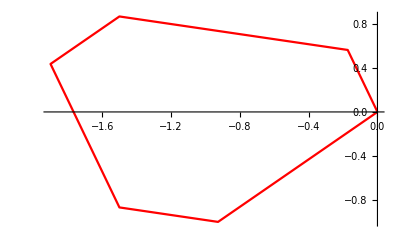

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
(*oj={bjx,bjy,bjz};*)
```

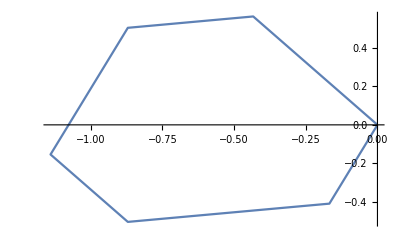

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
ListLinePlot[(p/.sub)[[;;, 1;;2]]]
(*pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
len
```

{l1→1.29872,l2→1.57164,l3→1.58122,l4→1.45458,l5→1.22907,l6→1.39188}

```mathematica
nsol[[1]]/60
```

42.8654

```mathematica
Timing[Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]]](*Residue check*)
```

{0.692624,{655.527,655.527,655.527,655.527,5.4313×10^17,5.4313×10^17,4.49807×10^17,4.49807×10^17,2.09836×10^-12,2.09836×10^-12,1.02358×10^-15,1.06985×10^19,1.06985×10^19,1.48253×10^19,1.48253×10^19,2.7398×10^-15,4.94211×10^16,4.94211×10^16,4.00425×10^16,4.00425×10^16,3.63311×10^17,3.63311×10^17,1.56242×10^17,1.56242×10^17,2.07407×10^-15,2.13971×10^16,2.13971×10^16,7.92079×10^16,7.92079×10^16,1.15911×10^-15,9.22025×10^16,9.22025×10^16,1.01804×10^17,1.01804×10^17,1.63652×10^17,1.63652×10^17,1.16805×10^17,1.16805×10^17,45.3568,45.3568,50.5654,50.5654,86449.1,86449.1,1.4535×10^8,1.4535×10^8,557068.,557068.,952057.,952057.,14.087,14.087,1.64802×10^16,1.64802×10^16,9.44212×10^-15,9.44212×10^-15,1.77982×10^-15,1.77982×10^-15,2.54142×10^-14,2.54142×10^-14,4.21124×10^7,4.21124×10^7,1.34722×10^-15,1.34722×10^-15,197482.,197482.,208495.,208495.,1.52731×10^-15,1.52731×10^-15,2.2679×10^-14,2.2679×10^-14,2.23273×10^18,2.23273×10^18,2.13275×10^18,2.13275×10^18,327218.,327218.,5.35968×10^19,5.35968×10^19,6.31061×10^19,6.31061×10^19,8.88178×10^-15,8.88178×10^-15,12.3195,12.3195,45.3524,45.3524,50.5682,50.5682,1.64802×10^16,1.64802×10^16,14.087,14.087,952057.,952057.,557068.,557068.,1.4535×10^8,1.4535×10^8,86449.1,86449.1,50.5654,50.5654,45.3568,45.3568,1.16805×10^17,1.16805×10^17,1.63652×10^17,1.63652×10^17,1.01804×10^17,1.01804×10^17,9.22025×10^16,9.22025×10^16,1.15911×10^-15,7.92079×10^16,7.92079×10^16,2.13971×10^16,2.13971×10^16,2.07407×10^-15,1.56242×10^17,1.56242×10^17,3.63311×10^17,3.63311×10^17,4.00425×10^16,4.00425×10^16,4.94211×10^16,4.94211×10^16,2.7398×10^-15,1.48253×10^19,1.48253×10^19,1.06985×10^19,1.06985×10^19,1.02358×10^-15,2.09836×10^-12,2.09836×10^-12,4.49807×10^17,4.49807×10^17,5.4313×10^17,5.4313×10^17,655.527,655.527,655.527,655.527}}

```mathematica
Export["fksol.m",nsol[[2]]]
```

fksol.m

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.nsol[[2]][[1]])] ]
```

655.527

```mathematica
(* The solutions which satisfy the constraints *)
fksol={};
For[i=1,i≤Length[nsol[[2]]],i++,
If[(Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.nsol[[2]][[i]])] ])<10^(-10),AppendTo[fksol,nsol[[2]][[i]]]]
]
```

```mathematica
fksol//Dimensions
```

{26,6}

```mathematica
Table[Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.fksol[[ii]])] ],{ii,26}] (* Residue check *)
```

{2.09836×10^-12,2.09836×10^-12,1.02358×10^-15,2.7398×10^-15,2.07407×10^-15,1.15911×10^-15,9.44212×10^-15,9.44212×10^-15,1.77982×10^-15,1.77982×10^-15,2.54142×10^-14,2.54142×10^-14,1.34722×10^-15,1.34722×10^-15,1.52731×10^-15,1.52731×10^-15,2.2679×10^-14,2.2679×10^-14,8.88178×10^-15,8.88178×10^-15,1.15911×10^-15,2.07407×10^-15,2.7398×10^-15,1.02358×10^-15,2.09836×10^-12,2.09836×10^-12}

```mathematica
Export["fksol.m",fksol]
```

fksol.m

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.288468,0.0979861,0.0922587,4.19814×10^-16,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.18135+8.56964×10^-7 ⅈ,-0.18135-8.56964×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.350057-1.5971×10^-9 ⅈ,-0.350057+1.5971×10^-9 ⅈ,3.25929,3.25929,-0.0994996,-0.0994996,-0.855175,-0.855175,5.51428,5.51428,-0.115132,-0.115132,-0.181348,-0.181348,-0.181352,-0.181352,-0.0936815,-0.0936815,3.05986,3.05986,-0.129623,-0.129623,-0.129623,-0.129623,-0.181349,-0.181349,7.71469,7.71469,7.71469,7.71469,-0.489099,-0.489099,-0.518214,-0.518214,0.,0.,0.,0.,-0.350057+1.5971×10^-9 ⅈ,-0.350057-1.5971×10^-9 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.18135-8.56964×10^-7 ⅈ,-0.18135+8.56964×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.19814×10^-16,0.0922587,0.0979861,0.288468,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(*Coefficient[Times@@(α{2,4,4,4,4,4}),α^6]
Coefficient[Times@@(α{2,3,3,3,3,3}),α^6]
Coefficient[Times@@(α{2,2,2,2,2,2}+β{0,2,2,2,2,2}),α^3 β^3]
Coefficient[Times@@(α{2,1,1,1,1,1}+β{0,2,2,2,2,2}),α^3 β^3]*)(*multi-homogenoeus Bezout number calculation for different grouping and formulation*)
```

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2,-28;;]];
```

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{7.92079×10^16,2.13971×10^16,2.13971×10^16,2.07407×10^-15,1.56242×10^17,1.56242×10^17,3.63311×10^17,3.63311×10^17,4.00425×10^16,4.00425×10^16,4.94211×10^16,4.94211×10^16,2.7398×10^-15,1.48253×10^19,1.48253×10^19,1.06985×10^19,1.06985×10^19,1.02358×10^-15,2.09836×10^-12,2.09836×10^-12,4.49807×10^17,4.49807×10^17,5.4313×10^17,5.4313×10^17,655.527,655.527,655.527,655.527}

### These are solutions for the center of the moving platform

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[({1,0,0}+{x,y,z}-Rmat.{0.5803,0,0}),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,28}];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→-2.56369×10^15+3.52586×10^15 ⅈ | y→3.96745×10^15+1.69241×10^15 ⅈ | z→-8.36803×10^14-2.77804×10^15 ⅈ | c1→0.278965+0.134284 ⅈ | c2→0.470314-0.828751 ⅈ | c3→-0.404683-0.870589 ⅈ
x→-2.45926×10^15-2.04869×10^15 ⅈ | y→2.51978×10^15-1.91848×10^15 ⅈ | z→-9.59182×10^13+2.12809×10^15 ⅈ | c1→0.278965-0.134284 ⅈ | c2→0.470314+0.828751 ⅈ | c3→-0.404683+0.870589 ⅈ
x→-2.45926×10^15+2.04869×10^15 ⅈ | y→2.51978×10^15+1.91848×10^15 ⅈ | z→-9.59182×10^13-2.12809×10^15 ⅈ | c1→0.278965+0.134284 ⅈ | c2→0.470314-0.828751 ⅈ | c3→-0.404683-0.870589 ⅈ
x→-0.216293 | y→0.430243 | z→1.0375 | c1→0.407839 | c2→0.606619 | c3→0.0922587
x→-7.44495×10^15-4.73704×10^15 ⅈ | y→4.3456×10^15+1.01172×10^16 ⅈ | z→-1.04115×10^16+7.61009×10^15 ⅈ | c1→0.506035-0.381721 ⅈ | c2→-1.32254+1.39882 ⅈ | c3→-1.28103-1.59493 ⅈ
x→-7.44495×10^15+4.73704×10^15 ⅈ | y→4.3456×10^15-1.01172×10^16 ⅈ | z→-1.04115×10^16-7.61009×10^15 ⅈ | c1→0.506035+0.381721 ⅈ | c2→-1.32254-1.39882 ⅈ | c3→-1.28103+1.59493 ⅈ
x→-7.99086×10^15-7.92334×10^15 ⅈ | y→2.66859×10^15+1.37859×10^16 ⅈ | z→-1.50387×10^16+6.65636×10^15 ⅈ | c1→0.506035-0.381721 ⅈ | c2→-1.32254+1.39882 ⅈ | c3→-1.28103-1.59493 ⅈ
x→-7.99086×10^15+7.92334×10^15 ⅈ | y→2.66859×10^15-1.37859×10^16 ⅈ | z→-1.50387×10^16-6.65636×10^15 ⅈ | c1→0.506035+0.381721 ⅈ | c2→-1.32254-1.39882 ⅈ | c3→-1.28103+1.59493 ⅈ
x→-6.63529×10^15-6.04323×10^15 ⅈ | y→7.2959×10^15-5.06212×10^15 ⅈ | z→5.32126×10^14-5.94934×10^15 ⅈ | c1→0.576301-0.808112 ⅈ | c2→0.249322+0.204538 ⅈ | c3→0.439065+0.944553 ⅈ
x→-6.63529×10^15+6.04323×10^15 ⅈ | y→7.2959×10^15+5.06212×10^15 ⅈ | z→5.32126×10^14+5.94934×10^15 ⅈ | c1→0.576301+0.808112 ⅈ | c2→0.249322-0.204538 ⅈ | c3→0.439065-0.944553 ⅈ
x→6.65113×10^15-3.8128×10^15 ⅈ | y→2.20566×10^15+7.25776×10^15 ⅈ | z→4.69808×10^15+1.99044×10^15 ⅈ | c1→0.576301-0.808112 ⅈ | c2→0.249322+0.204538 ⅈ | c3→0.439065+0.944553 ⅈ
x→6.65113×10^15+3.8128×10^15 ⅈ | y→2.20566×10^15-7.25776×10^15 ⅈ | z→4.69808×10^15-1.99044×10^15 ⅈ | c1→0.576301+0.808112 ⅈ | c2→0.249322-0.204538 ⅈ | c3→0.439065-0.944553 ⅈ
x→0.643707 | y→-0.352394 | z→0.868577 | c1→0.63715 | c2→-0.397368 | c3→0.0979861
x→ComplexInfinity | y→ComplexInfinity | z→ComplexInfinity | c1→0.736469-0.310898 ⅈ | c2→0.189026+1.21878 ⅈ | c3→-0.0664848+0.0212803 ⅈ
x→ComplexInfinity | y→ComplexInfinity | z→ComplexInfinity | c1→0.736469+0.310898 ⅈ | c2→0.189026-1.21878 ⅈ | c3→-0.0664848-0.0212803 ⅈ
x→1.91139×10^17+7.52241×10^16 ⅈ | y→-2.59049×10^16+1.29009×10^17 ⅈ | z→7.65818×10^16-1.44111×10^17 ⅈ | c1→0.736469-0.310898 ⅈ | c2→0.189026+1.21878 ⅈ | c3→-0.0664848+0.0212803 ⅈ
x→1.91139×10^17-7.52241×10^16 ⅈ | y→-2.59049×10^16-1.29009×10^17 ⅈ | z→7.65818×10^16+1.44111×10^17 ⅈ | c1→0.736469+0.310898 ⅈ | c2→0.189026-1.21878 ⅈ | c3→-0.0664848-0.0212803 ⅈ
x→-0.566749 | y→-0.473614 | z→-0.658513 | c1→1.14748 | c2→0.391681 | c3→0.288468
x→-0.0591115+0.129136 ⅈ | y→-0.14228+0.0287645 ⅈ | z→-0.104719+0.313473 ⅈ | c1→1.2694-0.183419 ⅈ | c2→0.428878-0.160995 ⅈ | c3→2.37803+0.145266 ⅈ
x→-0.0591115-0.129136 ⅈ | y→-0.14228-0.0287645 ⅈ | z→-0.104719-0.313473 ⅈ | c1→1.2694+0.183419 ⅈ | c2→0.428878+0.160995 ⅈ | c3→2.37803-0.145266 ⅈ
x→1.63105×10^16-1.5126×10^16 ⅈ | y→-8.71957×10^15-1.05394×10^16 ⅈ | z→-1.23986×10^16-1.24865×10^16 ⅈ | c1→1.45209-0.650558 ⅈ | c2→-0.321941-0.123527 ⅈ | c3→-0.518754-1.74437 ⅈ
x→1.63105×10^16+1.5126×10^16 ⅈ | y→-8.71957×10^15+1.05394×10^16 ⅈ | z→-1.23986×10^16+1.24865×10^16 ⅈ | c1→1.45209+0.650558 ⅈ | c2→-0.321941+0.123527 ⅈ | c3→-0.518754+1.74437 ⅈ
x→1.85964×10^16+5.27995×10^13 ⅈ | y→6.78779×10^14-1.14152×10^16 ⅈ | z→-4.60205×10^14-1.47033×10^16 ⅈ | c1→1.45209-0.650558 ⅈ | c2→-0.321941-0.123527 ⅈ | c3→-0.518754-1.74437 ⅈ
x→1.85964×10^16-5.27995×10^13 ⅈ | y→6.78779×10^14+1.14152×10^16 ⅈ | z→-4.60205×10^14+1.47033×10^16 ⅈ | c1→1.45209+0.650558 ⅈ | c2→-0.321941+0.123527 ⅈ | c3→-0.518754+1.74437 ⅈ
x→0.4197+2.77556×10^-17 ⅈ | y→0.+0. ⅈ | z→0.+0. ⅈ | c1→2.74338-17.4536 ⅈ | c2→0.+0. ⅈ | c3→0.+0. ⅈ
x→0.4197-2.77556×10^-17 ⅈ | y→0.+0. ⅈ | z→0.+0. ⅈ | c1→2.74338+17.4536 ⅈ | c2→0.+0. ⅈ | c3→0.+0. ⅈ
x→0.4197+0. ⅈ | y→0.+0. ⅈ | z→0.+0. ⅈ | c1→2.74338-17.4536 ⅈ | c2→0.+0. ⅈ | c3→0.+0. ⅈ
x→0.4197+0. ⅈ | y→0.+0. ⅈ | z→0.+0. ⅈ | c1→2.74338+17.4536 ⅈ | c2→0.+0. ⅈ | c3→0.+0. ⅈ)

```mathematica
Chop[transformedsol]//MatrixForm
```

(x→-2.56369×10^15+3.52586×10^15 ⅈ | y→3.96745×10^15+1.69241×10^15 ⅈ | z→-8.36803×10^14-2.77804×10^15 ⅈ | c1→0.278965+0.134284 ⅈ | c2→0.470314-0.828751 ⅈ | c3→-0.404683-0.870589 ⅈ
x→-2.45926×10^15-2.04869×10^15 ⅈ | y→2.51978×10^15-1.91848×10^15 ⅈ | z→-9.59182×10^13+2.12809×10^15 ⅈ | c1→0.278965-0.134284 ⅈ | c2→0.470314+0.828751 ⅈ | c3→-0.404683+0.870589 ⅈ
x→-2.45926×10^15+2.04869×10^15 ⅈ | y→2.51978×10^15+1.91848×10^15 ⅈ | z→-9.59182×10^13-2.12809×10^15 ⅈ | c1→0.278965+0.134284 ⅈ | c2→0.470314-0.828751 ⅈ | c3→-0.404683-0.870589 ⅈ
x→-0.216293 | y→0.430243 | z→1.0375 | c1→0.407839 | c2→0.606619 | c3→0.0922587
x→-7.44495×10^15-4.73704×10^15 ⅈ | y→4.3456×10^15+1.01172×10^16 ⅈ | z→-1.04115×10^16+7.61009×10^15 ⅈ | c1→0.506035-0.381721 ⅈ | c2→-1.32254+1.39882 ⅈ | c3→-1.28103-1.59493 ⅈ
x→-7.44495×10^15+4.73704×10^15 ⅈ | y→4.3456×10^15-1.01172×10^16 ⅈ | z→-1.04115×10^16-7.61009×10^15 ⅈ | c1→0.506035+0.381721 ⅈ | c2→-1.32254-1.39882 ⅈ | c3→-1.28103+1.59493 ⅈ
x→-7.99086×10^15-7.92334×10^15 ⅈ | y→2.66859×10^15+1.37859×10^16 ⅈ | z→-1.50387×10^16+6.65636×10^15 ⅈ | c1→0.506035-0.381721 ⅈ | c2→-1.32254+1.39882 ⅈ | c3→-1.28103-1.59493 ⅈ
x→-7.99086×10^15+7.92334×10^15 ⅈ | y→2.66859×10^15-1.37859×10^16 ⅈ | z→-1.50387×10^16-6.65636×10^15 ⅈ | c1→0.506035+0.381721 ⅈ | c2→-1.32254-1.39882 ⅈ | c3→-1.28103+1.59493 ⅈ
x→-6.63529×10^15-6.04323×10^15 ⅈ | y→7.2959×10^15-5.06212×10^15 ⅈ | z→5.32126×10^14-5.94934×10^15 ⅈ | c1→0.576301-0.808112 ⅈ | c2→0.249322+0.204538 ⅈ | c3→0.439065+0.944553 ⅈ
x→-6.63529×10^15+6.04323×10^15 ⅈ | y→7.2959×10^15+5.06212×10^15 ⅈ | z→5.32126×10^14+5.94934×10^15 ⅈ | c1→0.576301+0.808112 ⅈ | c2→0.249322-0.204538 ⅈ | c3→0.439065-0.944553 ⅈ
x→6.65113×10^15-3.8128×10^15 ⅈ | y→2.20566×10^15+7.25776×10^15 ⅈ | z→4.69808×10^15+1.99044×10^15 ⅈ | c1→0.576301-0.808112 ⅈ | c2→0.249322+0.204538 ⅈ | c3→0.439065+0.944553 ⅈ
x→6.65113×10^15+3.8128×10^15 ⅈ | y→2.20566×10^15-7.25776×10^15 ⅈ | z→4.69808×10^15-1.99044×10^15 ⅈ | c1→0.576301+0.808112 ⅈ | c2→0.249322-0.204538 ⅈ | c3→0.439065-0.944553 ⅈ
x→0.643707 | y→-0.352394 | z→0.868577 | c1→0.63715 | c2→-0.397368 | c3→0.0979861
x→ComplexInfinity | y→ComplexInfinity | z→ComplexInfinity | c1→0.736469-0.310898 ⅈ | c2→0.189026+1.21878 ⅈ | c3→-0.0664848+0.0212803 ⅈ
x→ComplexInfinity | y→ComplexInfinity | z→ComplexInfinity | c1→0.736469+0.310898 ⅈ | c2→0.189026-1.21878 ⅈ | c3→-0.0664848-0.0212803 ⅈ
x→1.91139×10^17+7.52241×10^16 ⅈ | y→-2.59049×10^16+1.29009×10^17 ⅈ | z→7.65818×10^16-1.44111×10^17 ⅈ | c1→0.736469-0.310898 ⅈ | c2→0.189026+1.21878 ⅈ | c3→-0.0664848+0.0212803 ⅈ
x→1.91139×10^17-7.52241×10^16 ⅈ | y→-2.59049×10^16-1.29009×10^17 ⅈ | z→7.65818×10^16+1.44111×10^17 ⅈ | c1→0.736469+0.310898 ⅈ | c2→0.189026-1.21878 ⅈ | c3→-0.0664848-0.0212803 ⅈ
x→-0.566749 | y→-0.473614 | z→-0.658513 | c1→1.14748 | c2→0.391681 | c3→0.288468
x→-0.0591115+0.129136 ⅈ | y→-0.14228+0.0287645 ⅈ | z→-0.104719+0.313473 ⅈ | c1→1.2694-0.183419 ⅈ | c2→0.428878-0.160995 ⅈ | c3→2.37803+0.145266 ⅈ
x→-0.0591115-0.129136 ⅈ | y→-0.14228-0.0287645 ⅈ | z→-0.104719-0.313473 ⅈ | c1→1.2694+0.183419 ⅈ | c2→0.428878+0.160995 ⅈ | c3→2.37803-0.145266 ⅈ
x→1.63105×10^16-1.5126×10^16 ⅈ | y→-8.71957×10^15-1.05394×10^16 ⅈ | z→-1.23986×10^16-1.24865×10^16 ⅈ | c1→1.45209-0.650558 ⅈ | c2→-0.321941-0.123527 ⅈ | c3→-0.518754-1.74437 ⅈ
x→1.63105×10^16+1.5126×10^16 ⅈ | y→-8.71957×10^15+1.05394×10^16 ⅈ | z→-1.23986×10^16+1.24865×10^16 ⅈ | c1→1.45209+0.650558 ⅈ | c2→-0.321941+0.123527 ⅈ | c3→-0.518754+1.74437 ⅈ
x→1.85964×10^16+5.27995×10^13 ⅈ | y→6.78779×10^14-1.14152×10^16 ⅈ | z→-4.60205×10^14-1.47033×10^16 ⅈ | c1→1.45209-0.650558 ⅈ | c2→-0.321941-0.123527 ⅈ | c3→-0.518754-1.74437 ⅈ
x→1.85964×10^16-5.27995×10^13 ⅈ | y→6.78779×10^14+1.14152×10^16 ⅈ | z→-4.60205×10^14+1.47033×10^16 ⅈ | c1→1.45209+0.650558 ⅈ | c2→-0.321941+0.123527 ⅈ | c3→-0.518754+1.74437 ⅈ
x→0.4197 | y→0 | z→0 | c1→2.74338-17.4536 ⅈ | c2→0 | c3→0
x→0.4197 | y→0 | z→0 | c1→2.74338+17.4536 ⅈ | c2→0 | c3→0
x→0.4197 | y→0 | z→0 | c1→2.74338-17.4536 ⅈ | c2→0 | c3→0
x→0.4197 | y→0 | z→0 | c1→2.74338+17.4536 ⅈ | c2→0 | c3→0)

```mathematica
roots = transformedsol
```

{{x→-2.56369×10^15+3.52586×10^15 ⅈ,y→3.96745×10^15+1.69241×10^15 ⅈ,z→-8.36803×10^14-2.77804×10^15 ⅈ,c1→0.278965+0.134284 ⅈ,c2→0.470314-0.828751 ⅈ,c3→-0.404683-0.870589 ⅈ},{x→-2.45926×10^15-2.04869×10^15 ⅈ,y→2.51978×10^15-1.91848×10^15 ⅈ,z→-9.59182×10^13+2.12809×10^15 ⅈ,c1→0.278965-0.134284 ⅈ,c2→0.470314+0.828751 ⅈ,c3→-0.404683+0.870589 ⅈ},{x→-2.45926×10^15+2.04869×10^15 ⅈ,y→2.51978×10^15+1.91848×10^15 ⅈ,z→-9.59182×10^13-2.12809×10^15 ⅈ,c1→0.278965+0.134284 ⅈ,c2→0.470314-0.828751 ⅈ,c3→-0.404683-0.870589 ⅈ},{x→-0.216293,y→0.430243,z→1.0375,c1→0.407839,c2→0.606619,c3→0.0922587},{x→-7.44495×10^15-4.73704×10^15 ⅈ,y→4.3456×10^15+1.01172×10^16 ⅈ,z→-1.04115×10^16+7.61009×10^15 ⅈ,c1→0.506035-0.381721 ⅈ,c2→-1.32254+1.39882 ⅈ,c3→-1.28103-1.59493 ⅈ},{x→-7.44495×10^15+4.73704×10^15 ⅈ,y→4.3456×10^15-1.01172×10^16 ⅈ,z→-1.04115×10^16-7.61009×10^15 ⅈ,c1→0.506035+0.381721 ⅈ,c2→-1.32254-1.39882 ⅈ,c3→-1.28103+1.59493 ⅈ},{x→-7.99086×10^15-7.92334×10^15 ⅈ,y→2.66859×10^15+1.37859×10^16 ⅈ,z→-1.50387×10^16+6.65636×10^15 ⅈ,c1→0.506035-0.381721 ⅈ,c2→-1.32254+1.39882 ⅈ,c3→-1.28103-1.59493 ⅈ},{x→-7.99086×10^15+7.92334×10^15 ⅈ,y→2.66859×10^15-1.37859×10^16 ⅈ,z→-1.50387×10^16-6.65636×10^15 ⅈ,c1→0.506035+0.381721 ⅈ,c2→-1.32254-1.39882 ⅈ,c3→-1.28103+1.59493 ⅈ},{x→-6.63529×10^15-6.04323×10^15 ⅈ,y→7.2959×10^15-5.06212×10^15 ⅈ,z→5.32126×10^14-5.94934×10^15 ⅈ,c1→0.576301-0.808112 ⅈ,c2→0.249322+0.204538 ⅈ,c3→0.439065+0.944553 ⅈ},{x→-6.63529×10^15+6.04323×10^15 ⅈ,y→7.2959×10^15+5.06212×10^15 ⅈ,z→5.32126×10^14+5.94934×10^15 ⅈ,c1→0.576301+0.808112 ⅈ,c2→0.249322-0.204538 ⅈ,c3→0.439065-0.944553 ⅈ},{x→6.65113×10^15-3.8128×10^15 ⅈ,y→2.20566×10^15+7.25776×10^15 ⅈ,z→4.69808×10^15+1.99044×10^15 ⅈ,c1→0.576301-0.808112 ⅈ,c2→0.249322+0.204538 ⅈ,c3→0.439065+0.944553 ⅈ},{x→6.65113×10^15+3.8128×10^15 ⅈ,y→2.20566×10^15-7.25776×10^15 ⅈ,z→4.69808×10^15-1.99044×10^15 ⅈ,c1→0.576301+0.808112 ⅈ,c2→0.249322-0.204538 ⅈ,c3→0.439065-0.944553 ⅈ},{x→0.643707,y→-0.352394,z→0.868577,c1→0.63715,c2→-0.397368,c3→0.0979861},{x→ComplexInfinity,y→ComplexInfinity,z→ComplexInfinity,c1→0.736469-0.310898 ⅈ,c2→0.189026+1.21878 ⅈ,c3→-0.0664848+0.0212803 ⅈ},{x→ComplexInfinity,y→ComplexInfinity,z→ComplexInfinity,c1→0.736469+0.310898 ⅈ,c2→0.189026-1.21878 ⅈ,c3→-0.0664848-0.0212803 ⅈ},{x→1.91139×10^17+7.52241×10^16 ⅈ,y→-2.59049×10^16+1.29009×10^17 ⅈ,z→7.65818×10^16-1.44111×10^17 ⅈ,c1→0.736469-0.310898 ⅈ,c2→0.189026+1.21878 ⅈ,c3→-0.0664848+0.0212803 ⅈ},{x→1.91139×10^17-7.52241×10^16 ⅈ,y→-2.59049×10^16-1.29009×10^17 ⅈ,z→7.65818×10^16+1.44111×10^17 ⅈ,c1→0.736469+0.310898 ⅈ,c2→0.189026-1.21878 ⅈ,c3→-0.0664848-0.0212803 ⅈ},{x→-0.566749,y→-0.473614,z→-0.658513,c1→1.14748,c2→0.391681,c3→0.288468},{x→-0.0591115+0.129136 ⅈ,y→-0.14228+0.0287645 ⅈ,z→-0.104719+0.313473 ⅈ,c1→1.2694-0.183419 ⅈ,c2→0.428878-0.160995 ⅈ,c3→2.37803+0.145266 ⅈ},{x→-0.0591115-0.129136 ⅈ,y→-0.14228-0.0287645 ⅈ,z→-0.104719-0.313473 ⅈ,c1→1.2694+0.183419 ⅈ,c2→0.428878+0.160995 ⅈ,c3→2.37803-0.145266 ⅈ},{x→1.63105×10^16-1.5126×10^16 ⅈ,y→-8.71957×10^15-1.05394×10^16 ⅈ,z→-1.23986×10^16-1.24865×10^16 ⅈ,c1→1.45209-0.650558 ⅈ,c2→-0.321941-0.123527 ⅈ,c3→-0.518754-1.74437 ⅈ},{x→1.63105×10^16+1.5126×10^16 ⅈ,y→-8.71957×10^15+1.05394×10^16 ⅈ,z→-1.23986×10^16+1.24865×10^16 ⅈ,c1→1.45209+0.650558 ⅈ,c2→-0.321941+0.123527 ⅈ,c3→-0.518754+1.74437 ⅈ},{x→1.85964×10^16+5.27995×10^13 ⅈ,y→6.78779×10^14-1.14152×10^16 ⅈ,z→-4.60205×10^14-1.47033×10^16 ⅈ,c1→1.45209-0.650558 ⅈ,c2→-0.321941-0.123527 ⅈ,c3→-0.518754-1.74437 ⅈ},{x→1.85964×10^16-5.27995×10^13 ⅈ,y→6.78779×10^14+1.14152×10^16 ⅈ,z→-4.60205×10^14+1.47033×10^16 ⅈ,c1→1.45209+0.650558 ⅈ,c2→-0.321941+0.123527 ⅈ,c3→-0.518754+1.74437 ⅈ},{x→0.4197+2.77556×10^-17 ⅈ,y→0.+0. ⅈ,z→0.+0. ⅈ,c1→2.74338-17.4536 ⅈ,c2→0.+0. ⅈ,c3→0.+0. ⅈ},{x→0.4197-2.77556×10^-17 ⅈ,y→0.+0. ⅈ,z→0.+0. ⅈ,c1→2.74338+17.4536 ⅈ,c2→0.+0. ⅈ,c3→0.+0. ⅈ},{x→0.4197+0. ⅈ,y→0.+0. ⅈ,z→0.+0. ⅈ,c1→2.74338-17.4536 ⅈ,c2→0.+0. ⅈ,c3→0.+0. ⅈ},{x→0.4197+0. ⅈ,y→0.+0. ⅈ,z→0.+0. ⅈ,c1→2.74338+17.4536 ⅈ,c2→0.+0. ⅈ,c3→0.+0. ⅈ}}

```mathematica
Join[{roots[[15]]},roots[[20;;23]], roots[[26;;]]]//Chop
```

{{x→ComplexInfinity,y→ComplexInfinity,z→ComplexInfinity,c1→0.736469+0.310898 ⅈ,c2→0.189026-1.21878 ⅈ,c3→-0.0664848-0.0212803 ⅈ},{x→-0.0591115-0.129136 ⅈ,y→-0.14228-0.0287645 ⅈ,z→-0.104719-0.313473 ⅈ,c1→1.2694+0.183419 ⅈ,c2→0.428878+0.160995 ⅈ,c3→2.37803-0.145266 ⅈ},{x→1.63105×10^16-1.5126×10^16 ⅈ,y→-8.71957×10^15-1.05394×10^16 ⅈ,z→-1.23986×10^16-1.24865×10^16 ⅈ,c1→1.45209-0.650558 ⅈ,c2→-0.321941-0.123527 ⅈ,c3→-0.518754-1.74437 ⅈ},{x→1.63105×10^16+1.5126×10^16 ⅈ,y→-8.71957×10^15+1.05394×10^16 ⅈ,z→-1.23986×10^16+1.24865×10^16 ⅈ,c1→1.45209+0.650558 ⅈ,c2→-0.321941+0.123527 ⅈ,c3→-0.518754+1.74437 ⅈ},{x→1.85964×10^16+5.27995×10^13 ⅈ,y→6.78779×10^14-1.14152×10^16 ⅈ,z→-4.60205×10^14-1.47033×10^16 ⅈ,c1→1.45209-0.650558 ⅈ,c2→-0.321941-0.123527 ⅈ,c3→-0.518754-1.74437 ⅈ},{x→0.4197,y→0,z→0,c1→2.74338+17.4536 ⅈ,c2→0,c3→0},{x→0.4197,y→0,z→0,c1→2.74338-17.4536 ⅈ,c2→0,c3→0},{x→0.4197,y→0,z→0,c1→2.74338+17.4536 ⅈ,c2→0,c3→0}}